# Analysis of Salmon data from Dorner et al. (2008)

## Pink Salmon

```mathematica
(* data in raw form (time, species, count) *)
rawPink=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transiitons_16/fish_project/data/data_dorner_2008/pink_data.csv"];
```

```mathematica
rawPink[[1;;10]]//TableForm
```

BY | Stock | Region | Area | S | R
1959 | Nooksack | Puget Sound | South | 30 | 197.7
1961 | Nooksack | Puget Sound | South | 100 | 630.69
1963 | Nooksack | Puget Sound | South | 150 | 33.72
1965 | Nooksack | Puget Sound | South | 15.25 | 75.46
1967 | Nooksack | Puget Sound | South | 20.38 | 45.23
1969 | Nooksack | Puget Sound | South | 22.82 | 111.51
1971 | Nooksack | Puget Sound | South | 64.06 | 163.7
1973 | Nooksack | Puget Sound | South | 42.35 | 113.34
1975 | Nooksack | Puget Sound | South | 37.9 | 56.82

```mathematica
(* add to the stock label whether even or odd years *)
For[i=2,i≤Length[rawPink],i++,
If[EvenQ[rawPink[[i,1]]],rawPink[[i,2]]=rawPink[[i,2]]<>" Even",
rawPink[[i,2]]=rawPink[[i,2]]<>" Odd"]]
```

```mathematica
stocksPink=Union[rawPink[[2;;,2]]]
```

{Afognak Even,Afognak Odd,AKPen NW Even,AKPen NW Odd,AKPen SE and Scentral Even,AKPen SE and Scentral Odd,AKPen SW and Unimak Even,AKPen SW and Unimak Odd,Alitak Even,Alitak Odd,Area 10 Even,Area 10 Odd,Area 2E Even,Area 2E Odd,Area 6 Even,Area 6 Odd,Area 8 Even,Area 8 Odd,Area 9 Even,Area 9 Odd,Chignik Bay Even,Chignik Bay Odd,Chignik Central Even,Chignik Central Odd,Chignik E Even,Chignik E Odd,Chignik W Even,Chignik W Odd,Cook Outer D. Even,Cook Outer D. Odd,Cook S D. Even,Cook S D. Odd,Dungeness Odd,Fraser Odd,Golovin Even,Golovin Odd,Hood Canal Odd,Humpy Cr. Even,Humpy Cr. Odd,Inner South Coast wo Fraser Even,Kamishak Even,Kamishak Odd,Kodiak Eside-Nend Even,Kodiak Eside-Nend Odd,Kodiak Mainland Even,Kodiak Mainland Odd,Kodiak Wside Even,Kodiak Wside Odd,Montague Even,Montague Odd,Moses Pt and Norton Bay Even,Moses Pt and Norton Bay Odd,Nome Even,Nome Odd,Nooksack Odd,Nushagak Even,Perryville Even,Perryville Odd,Puyallup Odd,PWS E D. Even,PWS E D. Odd,PWS SE D. Even,PWS SE D. Odd,SEAK N Inside Even,SEAK N Inside Odd,SEAK N Outside Even,SEAK N Outside Odd,SEAK S Even,SEAK S Odd,Situk R. Even,Situk R. Odd,Skagit Odd,Snohomish Odd,Stillaguamish Odd,Unalakleet Even,Unalakleet Odd}

```mathematica
(* number of stocks (even and odd year stocks counted separately *)
numStocks=Length[stocksPink]
```

76

```mathematica
(* pinkData provides the data partitioned by stocks *)
pinkData=Table[Cases[rawPink,{_,stocksPink[[i]],_,_,_,_}],{i,1,numStocks}];
```

```mathematica
(* log plots of population data *)
logPlots=GraphicsGrid[
Table[{
(* plot *)
ListLinePlot[{pinkData[[i,;;,1]],Log[pinkData[[i,;;,6]]]}//Transpose,PlotLabel->stocksPink[[i]],PlotRange->{{1977,1995},{0,10}}],
(* psd  *)
Plot[Evaluate@PowerSpectralDensity[Log[pinkData[[i,;;,6]]],ω,5],{ω,-π,π},Filling->Axis,PlotRange->All]
},
{i,1,5}]
];
```

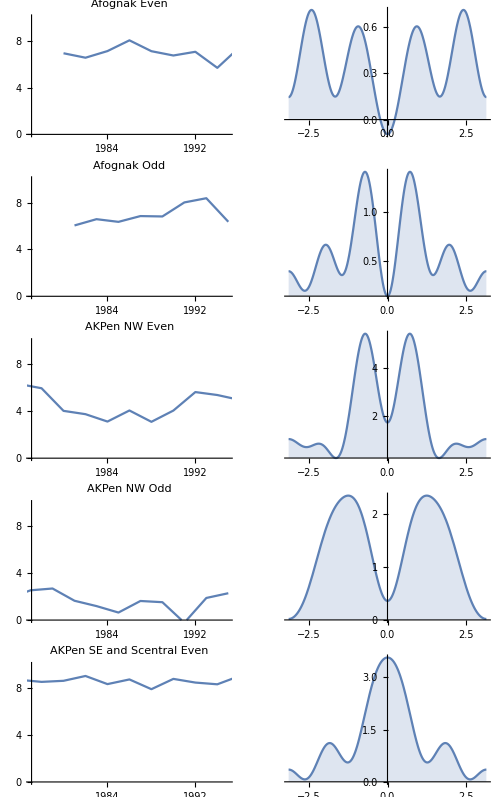

```mathematica
Show[logPlots,ImageSize->500]
```